```mathematica
Homework for 
       Chapter 6-1&6-2
```

# 2012311804 이병호/2016314728 정재헌

```mathematica
Quit
```

(#1) 다음 초기치 문제의  해를 구하시오.
                                       y''+5y'+5y=δ(t-2)-3δ(t-5)             with     y(0)=y'(0)=0.       
       여기서 δ(t)=DiracDelta[t]이다.

```mathematica
DSolve[{y''[t]+5y'[t]+5y[t]==DiracDelta[t-2]-3DiracDelta[t-5],y[0]==0,y'[0]==0},y[t],t]//Simplify
```

{{y[t]→1/(√5)(-3 ⅇ^(-1/2 (5+√5) (-5+t)) (-1+ⅇ^(√5 (-5+t))) HeavisideTheta[-5+t]+ⅇ^(-1/2 (5+√5) (-2+t)) (-1+ⅇ^(√5 (-2+t))) HeavisideTheta[-2+t])}}

(#2) 다음 초기치 문제의 해를 구하시오.
                                     y''+y'+15y=1-U(t-2)     with     y(0)=y'(0)=0.    
         여기서  U(t)=UnitStep[t] 혹은 HeavisideTheta[t]이다. Laplace 변환과 DSolve로 구한 solution을 비교하시오.

```mathematica
LaplaceTransform[y''[t]+y'[t]+15y[t]==1-UnitStep[t-2],t,s]
```

15 LaplaceTransform[y[t],t,s]+s LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-y[0]-s y[0]-y'[0]==1/s-ⅇ^(-2 s)/s

```mathematica
Solve[%,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(ⅇ^(-2 s) (-1+ⅇ^(2 s)+ⅇ^(2 s) s y[0]+ⅇ^(2 s) s^2 y[0]+ⅇ^(2 s) s y'[0]))/(s (15+s+s^2))}}

```mathematica
%⟦1⟧/.{y[0]->0,y'[0]->0}
```

{LaplaceTransform[y[t],t,s]→(ⅇ^(-2 s) (-1+ⅇ^(2 s)))/(s (15+s+s^2))}

```mathematica
InverseLaplaceTransform[LaplaceTransform[y[t],t,s]/.%,s,t]
```

1/885 ⅇ^(-t/2) (59 ⅇ^(t/2)-59 Cos[(√59 t)/2]+HeavisideTheta[-2+t] (-59 ⅇ^(t/2)+59 ⅇ Cos[1/2 √59 (-2+t)]+√59 ⅇ Sin[1/2 √59 (-2+t)])-√59 Sin[(√59 t)/2])

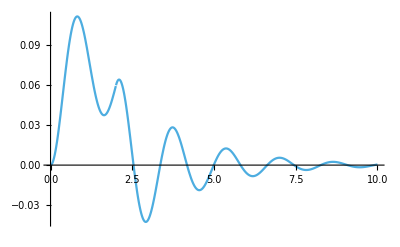

```mathematica
Plot[%,{t,0,10}]
```

## : Laplace 변환으로 구한 solution

```mathematica
DSolve[{y''[t]+y'[t]+15y[t]==1-UnitStep[t-2],y'[0]==0,y[0]==0},y[t],t] // Simplify
```

{{y[t]→1/885 ⅇ^(-t/2) (59 ⅇ Cos[1/2 √59 (-2+t)]-59 Cos[(√59 t)/2]+√59 ⅇ Sin[1/2 √59 (-2+t)]-√59 Sin[(√59 t)/2]+(59 ⅇ^(t/2)-59 ⅇ Cos[1/2 √59 (-2+t)]-√59 ⅇ Sin[1/2 √59 (-2+t)]) UnitStep[2-t])}}

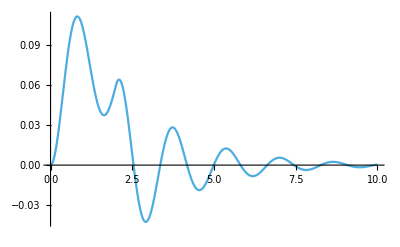

```mathematica
Plot[%[[1,1,2]],{t,0,10}]
```

## : Dsolve로 구한 solution

(#3) 다음의 미분적분방정식(integro-differential equation)을 Laplace 변환을 이용하여 그 해를 구하시오.
                         y'(t)+y(t)+∫_0^t y(u)ⅆu=1          with     y(0)=0.

```mathematica
LaplaceTransform[y'[t]+y[t]+∫_0^t y[u]ⅆu==1,t,s]
```

LaplaceTransform[y[t],t,s]+LaplaceTransform[y[t],t,s]/s+s LaplaceTransform[y[t],t,s]-y[0]==1/s

```mathematica
Solve[%,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(1+s y[0])/(1+s+s^2)}}

```mathematica
%⟦1⟧/.{y[0]->0}
```

{LaplaceTransform[y[t],t,s]→1/(1+s+s^2)}

```mathematica
InverseLaplaceTransform[LaplaceTransform[y[t],t,s]/.%,s,t]
```

(2 ⅇ^(-t/2) Sin[(√3 t)/2])/(√3)

(#4-1) 다음  함수 f(x)=4x(1-x), x∈[0,1]의 Fourier sine series 계수를 구하시오. 이 계수들의 감소율을 논하시오.                                               (plotting 필요)

```mathematica
f[x_]:=4x(1-x)
```

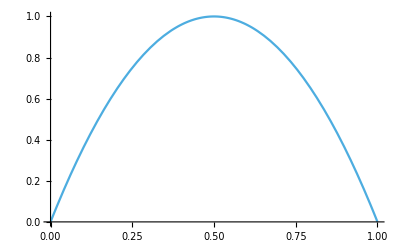

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
b[n_]:=2∫_0^1 4x(1-x)Sin[n π x]ⅆx
```

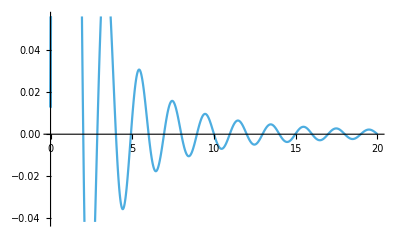

```mathematica
output1=Plot[b[n],{n,0,20}]
```

```mathematica
Limit[b[n],n->Infinity]
```

0

```mathematica
Table[b[n],{n,1,10}]
```

{32/π^3,0,32/(27 π^3),0,32/(125 π^3),0,32/(343 π^3),0,32/(729 π^3),0}

```mathematica
b[n]=32/(n^3*π^3) (n=odd)
b[n]=0 (n=even)
이므로, 따라서 이 계수들의 감소율은 n^3/(n+1)^3 이다.
```

(#4-2) 위  함수 의 Fourier cosine series 계수를 구하시오. 이 계수들과  문제 (1)의 계수와 비교하여 논하시오. (plotting 필요)

```mathematica
Quit
```

```mathematica
a[n_]:=2 ∫_0^1 4x(1-x)Cos[n π x]ⅆx
```

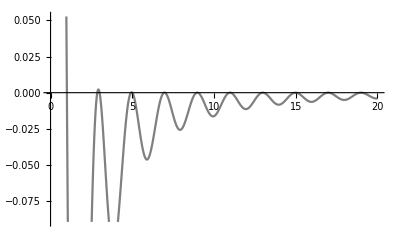

```mathematica
output2=Plot[a[n],{n,0,20}, PlotStyle->Gray]
```

```mathematica
Limit[a[n],n->Infinity]
```

0

```mathematica
Table[a[n],{n,1,20}]
```

{0,-4/π^2,0,-1/π^2,0,-4/(9 π^2),0,-1/(4 π^2),0,-4/(25 π^2),0,-1/(9 π^2),0,-4/(49 π^2),0,-1/(16 π^2),0,-4/(81 π^2),0,-1/(25 π^2)}

a[n] = 0 (n : odd)
a[n] = -4/((2 k - 1)^2*π^2) (n = 4 k - 2)
a[n] = -1/((2 k - 1)^2*π^2) (n = 4 k) 이므로,
따라서 이 계수들의 감소율은 (2 k - 1)^3/(2 k + 1)^3 이다.

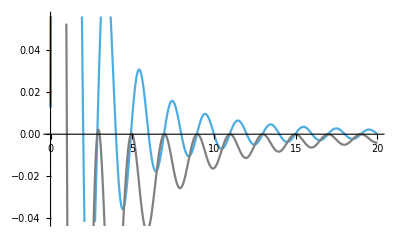

```mathematica
Show[output1, output2]
```

(#5) 다음 함수  g(x)=ⅇ^x,  x∈[-π,π] 를 적절히 나타내기 위해 얼마나 많은 Fourier series 계수가  필요한지를 구하고  주어진 함수와 얻어진 Fourier series를  도시(plot)하고 그 차이(오차)를 plotting하시오.

```mathematica
clear[*]
```

```mathematica
g[x_]:=ⅇ^x
```

```mathematica
G[n_]=FourierTrigSeries[g[x],x,n]
```

FourierTrigSeries[ⅇ^x,x,n]

```mathematica
G10=FourierTrigSeries[ⅇ^x,x,10];
```

```mathematica
G20=FourierTrigSeries[ⅇ^x,x,20];
```

```mathematica
G30=FourierTrigSeries[ⅇ^x,x,30];
```

```mathematica
G40=FourierTrigSeries[ⅇ^x,x,40];
```

```mathematica
G50=FourierTrigSeries[ⅇ^x,x,50];
```

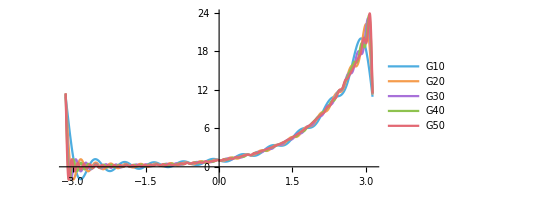

```mathematica
Plot[Evaluate[{G10,G20,G30,G40,G50}],{x,-π,π},PlotLegends->{"G10","G20","G30","G40","G50"}, AspectRatio-> 0.5]
```

즉 Fourier series 계수가 50 정도면 g (x) 를 충분히 나타낼 수 있다.

오차를 plotting 해보면, 다음과 같다

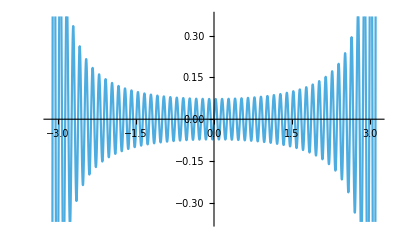

```mathematica
Plot[g[x]-G50, {x,-π,π}]
```